```mathematica
Quit[]
```

### 1.1 some parameters

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\PythonTemp\NSPBGW\code00

```mathematica
Msun=1.98847*10^30;                      (* Mass of the sun*)
Mpc=3.085677581*10^22;               (* million par second *)
pc=3.085677581*10^16;                  (* parsecond *)
yt=365*3600*24;
ly=365*3600*24*c;                          (* light year *)
Mly=10^6*365*24*3600*c;          (* million light year *)
H0=67.9*10^3/Mpc;                    (* Hubble constant *)
c=299792458;                                 (* Speed of light *)
Gn=6.67408*10^-11;(* Gravitational constant *)
```

```mathematica
a1=3.916;        b1=4.078;             c1= 4.857;
a2=7.701;        b2= 7.587;            c2= 6.981;
a3=0.00858;   b3= 0.00839;        c3= 0.00706;
a4=0.22114;   b4= 0.21695;        c4= 0.19351;
a5=3.269;        b5= 3.614;            c5= 4.085;
a6=11.964;      b6= 11.942;         c6= 12.065;
a7=13.349;      b7= 13.751;         c7= 10.521;
a8=1.3683;      b8= 1.3373;         c8= 1.5905;
a9=3.254;        b9= 3.606;            c9= 4.104;
a10=−12.953; b10=−22.996;     c10=−28.726;
a11=0.9237;    b11= 1.6229;       c11= 2.0845;
a12=6.20;         b12= 4.88;           c12= 4.89;
a13=14.383;    b13= 14.274;       c13= 14.302;
a14=16.693;    b14= 23.560;       c14= 22.881;
a15=−1.0514; b15=−1.5564;     c15=−1.7690;
a16=2.486 ;     b16=2.095;          c16= 0.989;
a17=15.362 ;   b17=15.294;       c17= 15.313;
a18=0.085;      b18= 0.084;        c18= 0.091;
a19=6.23;        b19= 6.36;           c19= 4.68;
a20=11.68;      b20= 11.67;        c20= 11.65;
a21=−0.029;   b21=−0.042;      c21=−0.086;
a22=20.1;        b22= 14.8;           c22= 10.0;
a23=14.19;      b23= 14.18;        c23= 14.15;
ρs=7.86*10^3;(*ρFe=7.86*10^3 kg/m^3*)
mn=1.4Msun; (* the NS parameters*)
```

### 1.2 the state of the NS, and give the relation between p and ρ

```mathematica
(*ra=10.74*10^3;*)
rb=11.74*10^3;
(*rc=12.57*10^3;*)
ξa=Log10[ρa1];
ks=(b1+b2 ξa+b3 ξa^3)/(1+b4 ξa)(Exp[b5(ξa-b6)]+1)^-1+(b7+b8 ξa)(Exp[b9(b6-ξa)]+1)^-1+(b10+b11 ξa)(Exp[b12(b13-ξa)]+1)^-1+(b14+b15 ξa)(Exp[b16(b17-ξa)]+1)^-1+b18(1+(b19(ξa-b20))^2)^-1+b21(1+(b22(ξa-b23))^2)^-1/.ρa1->10^-3 ρs;
ps=0.1*10^ks;
ζ[ρ_]:=(b1+b2 ξ[ρ]+b3 ξ[ρ]^3)/(1+b4 ξ[ρ])(Exp[b5(ξ[ρ]-b6)]+1)^-1+(b7+b8 ξ[ρ])(Exp[b9(b6-ξ[ρ])]+1)^-1+(b10+b11 ξ[ρ])(Exp[b12(b13-ξ[ρ])]+1)^-1+(b14+b15 ξ[ρ])(Exp[b16(b17-ξ[ρ])]+1)^-1+b18(1+(b19(ξ[ρ]-b20))^2)^-1+b21(1+(b22(ξ[ρ]-b23))^2)^-1
ξ[ρ_]:=Log10[10^-3 ρ];
pa[ρ_]:=10^ ζ[ρ]/10;
```

### 1.3 solve the result of the p,ρ,m from the equation

```mathematica
(* equation for the p,ρ,m*)
dpadρ[ρ_]:=Evaluate[D[pa[ρ],ρ]];
(*dpadr[r_]:=-(ρ[r]+pa[ρ[r]]/c^2)(Gn( m[r]+4π r^3 pa[ρ[r]]/c^2))/(r(r-2 Gn m[r]/c^2));*)
dpadr[r_]:=-(Gn m[r]ρ[r])/r^2;
dρdr[r_]:=dpadr[r] dpadρ[ρ[r]]^-1;
dmr[r_]:=4π r^2 ρ[r];
```

```mathematica
Res=Flatten[NDSolve[{m'[r]==dmr[r],ρ'[r]==dρdr[r],
ρ[10^-15]==1.18*10^14 ρs,m[10^-15]==0},{m,ρ},
{r,10^-8,11741.27835589},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]];
```

```mathematica
m1[r_]=m[r]/.Res;
ρ1[r_]=ρ[r]/.Res;
dm1dr[r_]:=4π r^2 ρ1[r];
dρ1dr[r_]:=dpadr[r] dpadρ[ρ[r]]^-1/.Res;
p1[r_]:=pa[ρ1[r]];
```

```mathematica
Clear[m1,ρ1,p1]
```

```mathematica
(*ra=r/.FindRoot[ρ1[r]==7860,{r,11740}]*)
ra = 11741.27835589099;
```

```mathematica
{m1[  11741]/Msun,m1[ 11740]/Msun,ρ1[rb],ρ1[ 11740],ρ1[11741.27835589]}
```

```mathematica
{1.407104680075818,1.4071046800756422,3.7328987225988156*^8,3.7328987225988156*^8,8065.126321444737}
```

{1.4071,1.4071,3.7329×10^8,3.7329×10^8,8065.13}

```mathematica
β1[r_]:=1/2 Log[(1-(2Gn m1[r])/(r c^2))^-1];
(*dα1dr[r_]:=(Gn (m1[r]+4π r^3 p1[r]/c^2))/(r^2 c^2(1-2Gn m1[r]/(r c^2)));*)
dα1dr[r_]:=(Gn (m1[r]))/(r^2 c^2);
(* the β1,B1 parameters can be directly calculate *)
B1[r_]:=(1-(2Gn m1[r])/(r c^2))^-1;
α1ra=1/2 Log[1-(2Gn m1[ra])/(ra c^2)]
NDSolve[{α'[r]==dα1dr[r],α[ra]==α1ra},{α},
{r,10^-10,ra},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
α1[r_]=α[r]/.%[[1,1]];
```

-0.418784

```mathematica
Export[ "model1alpha.txt", Table[N[{10^logr,α1[10^logr],dα1dr[10^logr]},16],{logr,-15,Log10[ra],20/100000}],"Table"]
Export[ "model1m.txt", Table[N[{10^logr,m1[10^logr],dm1dr[10^logr]},16],{logr,-15,Log10[ra],20/100000}],"Table"]
Export[ "model1rho.txt", Table[N[{10^logr,ρ1[10^logr],dρ1dr[10^logr]},16],{logr,-15,Log10[ra],20/100000}],"Table"]
```

model1alpha.txt

model1m.txt

model1rho.txt

```mathematica
Export[ "Newtonmodel1alpha.txt", Table[N[{10^logr,α1[10^logr],dα1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
Export[ "Newtonmodel1m.txt", Table[N[{10^logr,m1[10^logr],dm1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
Export[ "Newtonmodel1rho.txt", Table[N[{10^logr,ρ1[10^logr],dρ1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
```

Newtonmodel1alpha.txt

Newtonmodel1m.txt

Newtonmodel1rho.txt

```mathematica
rk=11741
ρk=ρ1[rk]
mk=m1[rk]
```

11741

5.8024×10^7

2.79799×10^30

```mathematica
Clear[rk,ρk,mk]
```

```mathematica
NDSolve[{m'[r]==dmr[r],ρ'[r]==dρdr[r],
ρ[rk]==ρk,m[rk]==mk},{m,ρ},
{r,0.1,rk},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
```

```mathematica
mk1[r_]=m[r]/.Res;
ρk1[r_]=ρ[r]/.Res;
pk1[r_]:=pa[ρk1[r]];
(* test*)
```

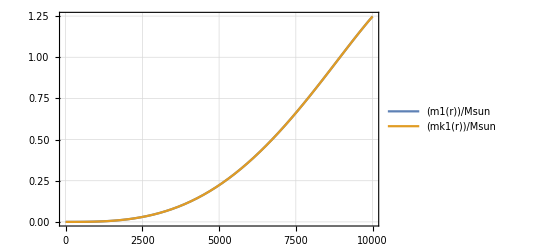

-Graphics-

-Graphics-

```mathematica
Plot[{m1[r]/Msun,mk1[r]/Msun},{r,1,10000},PlotTheme->"Detailed"]
Plot[{(*ρ1[r],*)ρk1[r]},{r,1,10000},PlotTheme->"Detailed"]
Plot[{p1[r],pk1[r]},{r,1,10000},PlotTheme->"Detailed"]
```